# Cálculo de pârametros unitários de uma linha de transmissão em circuito duplo

## Antonio Carlos S Lima EEE457 - Transmissão de Energia Elétrica 2021/2

## Início

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Dropbox/UFRJ/cursos/EEE457-Transmissão_Energia_Elétrica/arquivos_Mma_EEE457

### Algumas constantes

```mathematica
μ= 4.0 π 10^-7;
ϵ= 8.854 10^-12;
σs=10.0^-3;
ℓ=80 10^3; (* comprimento do circuito *)
```

cabos pararraios possuem permeabilidade magnética relativa próximo a 100

```mathematica
μr= 90.0;
```

## Circuito 138kV

Coordenadas dos condutores

```mathematica
xc={-4,-4,-4,4,4,4,-4.5,4.5};
yc={37.35,31.35,25.35,25.35,31.35, 37.35,42.05,42.05};
```

Dados condutores de fase

```mathematica
rf=0.013265;
rint=7.05*10^-3;
Rdc=0.0007998;
```

Dados dos cabos pararraios

```mathematica
rpr=4.57*10^-3;
Rdcpr=4.19*10^-3;
```

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},{0.09,0.20}]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,AspectRatio-> 0.5,PlotRange->{{-5,5},{5,50.}},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,FrameLabel->{Style["Distance [m]",Bold,18],Style["Distance [m]",Bold,18]}]
```

-Graphics-

## Função para cálculo das matrizes

faz parte do arquivo LineCableParam2020.wl

```mathematica
(* impedancia interna de condutores tubulares *)
ZintTubo[Omega_, Rhoc_, rf_, rint_, Mur_: 1, Mu_: (4.*Pi)/10^7] := 
 With[{Etac = N[Sqrt[(I*Omega*Mur*Mu)/Rhoc]], ri = rint + 10^-6}, 
  With[{Den = 
     BesselK[1, Etac*ri]*BesselI[1, Etac*rf] - 
      BesselK[1, Etac*rf]*BesselI[1, Etac*ri], 
    Num = BesselK[1, Etac*ri]*BesselI[0, Etac*rf] + 
      BesselK[0, Etac*rf]*BesselI[1, Etac*ri]}, ((Rhoc*Etac)*
      Num)/((2*Pi*rf)*Den)]]
      
(* impedancia interna de condutor sem alma de aco *)
(* impedancia interna de condutores cilindricos *) 
(*Mur=90 para cables de aco*)    
Zin[Omega_, Rhopr_, rpr_, Mur_:90, Mu_:(4*Pi)/10^7] := 
    With[{Etapr = Sqrt[(I*Omega*Mu*Mur)/Rhopr]}, 
         ((Etapr*Rhopr)*BesselI[0, Etapr*rpr])/((2*Pi*rpr)*BesselI[1,Etapr*rpr])]
```

```mathematica
(* internal impedance of cylindrical conductors *)
zintc= Compile[{{omega, _Complex}, {Rhoc, _Real}, {rf, _Real}, {ri,_Real}, {Mur, _Real}},
 ZintTubo[omega, Rhoc, rf, ri, Mur]];
 
zic= Compile[{{omega,_Complex},{rhoc, _Real},{rf, _Real}, {mur,_Real}},
	 Zin[omega, rhoc, rf, mur]];
```

```mathematica
(*  ground wires are not explicitly considered so we include their effects via Kron Reduction -- matrizes devem estar no formato de impedancia *)        
eliprc = Compile[{{m,_Complex,2},{nc,_Integer},{np,_Integer}},
	            Take[Inverse[m], nc - np, nc - np]
	            ];
```

```mathematica
(* case  2: ground wires and unbundled conductors *)
cZYlt[omega_,(x_)?VectorQ, (y_)?VectorQ, sigmas_, rdc_,rf_,rint_, npr_, rdcpr_, rpr_]:=
    Module[{mu=4*Pi*10^-7, eps=8.854*10^-12, nc=Length[x],  nf, rhoc, rhopr, mp, zin, ze, Z1, Y1},
    	
    nf= IntegerPart[(nc-npr)];
    rhoc= rdc*Pi*(rf^2-rint^2);
    rhopr= rdcpr*Pi*rpr^2;
   
   If[ rint != 0, 
   zin= DiagonalMatrix[
   	    Join[zintc[omega, rhoc, rf, rint, 1] Table[1, {i, nc - npr}], 
             zic[omega, rhopr, rpr, 90] Table[1, {i, npr}]]
             ],
   zin= DiagonalMatrix[
   	    Join[zic[omega, rhoc, rf, 1] Table[1, {i, nc - npr}], 
             zic[omega, rhopr, rpr,90] Table[1, {i, npr}]]
             ];
   ];
   
             
   ze= I omega mu/(2 Pi) With[{p = Sqrt[1/(I*omega*mu*sigmas)]}, 
         Table[If[i != j, 
         	  (Log[((x[[i]] - x[[j]])^2 + (2*p + y[[i]] + y[[j]])^2)/((x[[i]] - x[[j]])^2 +(y[[i]] - y[[j]])^2)])/(2), 
              If[i <= nc - npr, 
               (Log[(2*(y[[i]] + p))/rf]), 
               (Log[(2*(y[[i]] + p))/rpr])]],
         {i, 1, nc}, 
         {j, 1, nc}]];
         
    Z1 = Inverse[eliprc[zin+ze, nc, npr]];     
         
    mp= Table[If[i != j, 
   	    (1/2)*Log[((x[[i]] - x[[j]])^2 + (y[[i]] + y[[j]])^2)/((x[[i]] - x[[j]])^2 + (y[[i]] - y[[j]])^2)], 
        If[i <= nc - npr, Log[(2*y[[i]])/rf], 
        Log[(2*y[[i]])/rpr]]],{i, 1, nc}, {j, 1, nc}];
          
    Y1=3.0*10^-12 DiagonalMatrix[Table[1,{nf}]] + I omega*2*Pi*eps* eliprc[mp, nc, npr];
          
    {Z1, Y1}       
];
```

## Cálculo das matrizes

```mathematica
ω= 2. π 60;
ρs= 1000.;
npr = 2;
```

```mathematica
{Zmat, Ymat} =cZYlt[ω,xc,yc,1/ρs, Rdc,rf,rint, npr, Rdcpr, rpr];
```

```mathematica
MatrixForm[Zmat 1000]
```

(0.909393+0.881242 ⅈ | 0.103855+0.413703 ⅈ | 0.100276+0.36456 ⅈ | 0.100191+0.35074 ⅈ | 0.103675+0.375279 ⅈ | 0.108928+0.387414 ⅈ
0.103855+0.413703 ⅈ | 0.898878+0.890525 ⅈ | 0.0957797+0.420964 ⅈ | 0.0957507+0.382463 ⅈ | 0.0988851+0.396459 ⅈ | 0.103675+0.375279 ⅈ
0.100276+0.36456 ⅈ | 0.0957797+0.420964 ⅈ | 0.892804+0.896043 ⅈ | 0.0928585+0.401952 ⅈ | 0.0957507+0.382463 ⅈ | 0.100191+0.35074 ⅈ
0.100191+0.35074 ⅈ | 0.0957507+0.382463 ⅈ | 0.0928585+0.401952 ⅈ | 0.892804+0.896043 ⅈ | 0.0957797+0.420964 ⅈ | 0.100276+0.36456 ⅈ
0.103675+0.375279 ⅈ | 0.0988851+0.396459 ⅈ | 0.0957507+0.382463 ⅈ | 0.0957797+0.420964 ⅈ | 0.898878+0.890525 ⅈ | 0.103855+0.413703 ⅈ
0.108928+0.387414 ⅈ | 0.103675+0.375279 ⅈ | 0.100191+0.35074 ⅈ | 0.100276+0.36456 ⅈ | 0.103855+0.413703 ⅈ | 0.909393+0.881242 ⅈ)

```mathematica
MatrixForm[Ymat 1000]
```

(3.×10^-9+3.00434×10^-6 ⅈ | 0.-4.76501×10^-7 ⅈ | 0.-2.0134×10^-7 ⅈ | 0.-1.34033×10^-7 ⅈ | 0.-2.30235×10^-7 ⅈ | 0.-3.29885×10^-7 ⅈ
0.-4.76501×10^-7 ⅈ | 3.×10^-9+3.0061×10^-6 ⅈ | 0.-5.01396×10^-7 ⅈ | 0.-2.49002×10^-7 ⅈ | 0.-3.15975×10^-7 ⅈ | 0.-2.30235×10^-7 ⅈ
0.-2.0134×10^-7 ⅈ | 0.-5.01396×10^-7 ⅈ | 3.×10^-9+2.91641×10^-6 ⅈ | 0.-3.87974×10^-7 ⅈ | 0.-2.49002×10^-7 ⅈ | 0.-1.34033×10^-7 ⅈ
0.-1.34033×10^-7 ⅈ | 0.-2.49002×10^-7 ⅈ | 0.-3.87974×10^-7 ⅈ | 3.×10^-9+2.91641×10^-6 ⅈ | 0.-5.01396×10^-7 ⅈ | 0.-2.0134×10^-7 ⅈ
0.-2.30235×10^-7 ⅈ | 0.-3.15975×10^-7 ⅈ | 0.-2.49002×10^-7 ⅈ | 0.-5.01396×10^-7 ⅈ | 3.×10^-9+3.0061×10^-6 ⅈ | 0.-4.76501×10^-7 ⅈ
0.-3.29885×10^-7 ⅈ | 0.-2.30235×10^-7 ⅈ | 0.-1.34033×10^-7 ⅈ | 0.-2.0134×10^-7 ⅈ | 0.-4.76501×10^-7 ⅈ | 3.×10^-9+3.00434×10^-6 ⅈ)

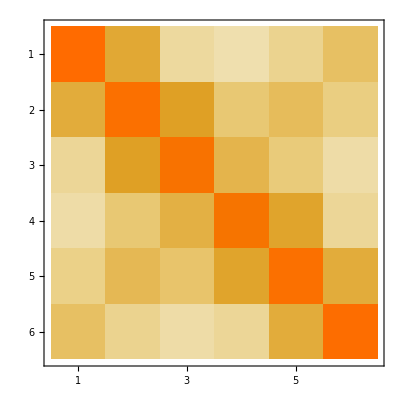

```mathematica
MatrixPlot[Abs@Zmat ]
```

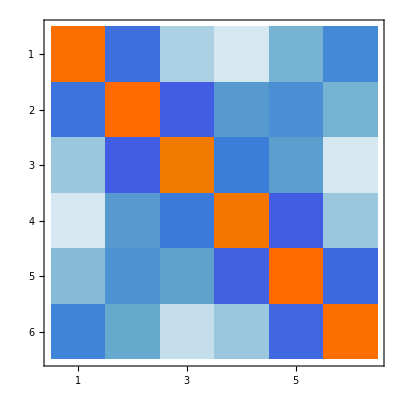

```mathematica
MatrixPlot[Im@Ymat ]
```

```mathematica
Ztotal= Zmat 1000 30.0;
```

```mathematica
a= Exp[I 120 Degree];
A={{1,1,1},{1,a^2,a},{1,a,a^2}};
MatrixForm[A]
```

(1 | 1 | 1
1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °)
1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °))

```mathematica
Aaug=ArrayFlatten[{{A,0},{0,A}}];
MatrixForm[Aaug]
```

(1 | 1 | 1 | 0 | 0 | 0
1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °) | 0 | 0 | 0
1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °) | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °)
0 | 0 | 0 | 1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °))

```mathematica
Z012=Inverse[Aaug].Zmat.Aaug;
MatrixForm[Z012]
```

(0.0011003+0.00168875 ⅈ | 0.0000192062-0.0000174116 ⅈ | -5.98107×10^-6-0.0000118382 ⅈ | 0.000299968+0.00113426 ⅈ | 6.18489×10^-6+4.62711×10^-6 ⅈ | -0.0000173528-3.73437×10^-6 ⅈ
-5.98107×10^-6-0.0000118382 ⅈ | 0.000800388+0.000489528 ⅈ | -0.000029639+0.000017521 ⅈ | 9.1475×10^-7-7.66982×10^-6 ⅈ | -3.01789×10^-7-0.0000180984 ⅈ | 0.0000221513-0.0000131952 ⅈ
0.0000192062-0.0000174116 ⅈ | 0.0000302925+0.0000168946 ⅈ | 0.000800388+0.000489528 ⅈ | 0.0000119105-0.0000131608 ⅈ | -0.000022503-0.000012586 ⅈ | -3.99708×10^-7-0.0000182261 ⅈ
0.000299968+0.00113426 ⅈ | 0.0000119105-0.0000131608 ⅈ | 9.1475×10^-7-7.66982×10^-6 ⅈ | 0.0011003+0.00168875 ⅈ | 0.0000132427+7.39348×10^-7 ⅈ | -0.000024682-7.92723×10^-6 ⅈ
-0.0000173528-3.73437×10^-6 ⅈ | -3.99708×10^-7-0.0000182261 ⅈ | 0.0000221513-0.0000131952 ⅈ | -0.000024682-7.92723×10^-6 ⅈ | 0.000800388+0.000489528 ⅈ | -0.0000297774+0.0000177867 ⅈ
6.18489×10^-6+4.62711×10^-6 ⅈ | -0.000022503-0.000012586 ⅈ | -3.01789×10^-7-0.0000180984 ⅈ | 0.0000132427+7.39348×10^-7 ⅈ | 0.0000299931+0.0000169076 ⅈ | 0.000800388+0.000489528 ⅈ)

```mathematica
MatrixForm[Abs[1000Z012[[1;;3,4;;6]]]]
```

(1.17326 | 0.00772418 | 0.0177501
0.00772418 | 0.0181009 | 0.0257836
0.0177501 | 0.0257836 | 0.0182305)

```mathematica
Y012=Inverse[Aaug].Ymat.Aaug;
MatrixForm[Y012]
```

(3.×10^-12+2.18946×10^-9 ⅈ | -5.35397×10^-11+6.85201×10^-11 ⅈ | 5.35397×10^-11+6.85201×10^-11 ⅈ | 1.45874×10^-26-7.53458×10^-10 ⅈ | -2.91735×10^-11-8.77521×10^-12 ⅈ | 2.91735×10^-11-8.77521×10^-12 ⅈ
5.35397×10^-11+6.85201×10^-11 ⅈ | 3.×10^-12+3.3687×10^-9 ⅈ | 1.84757×10^-10-9.39554×10^-11 ⅈ | 6.98719×10^-12+2.96526×10^-11 ⅈ | -5.93342×10^-12+8.47087×10^-11 ⅈ | -1.21406×10^-10+7.0094×10^-11 ⅈ
-5.35397×10^-11+6.85201×10^-11 ⅈ | -1.84757×10^-10-9.39554×10^-11 ⅈ | 3.×10^-12+3.3687×10^-9 ⅈ | -6.98719×10^-12+2.96526×10^-11 ⅈ | 1.21406×10^-10+7.0094×10^-11 ⅈ | 5.93342×10^-12+8.47087×10^-11 ⅈ
1.17432×10^-26-7.53458×10^-10 ⅈ | -6.98719×10^-12+2.96526×10^-11 ⅈ | 6.98719×10^-12+2.96526×10^-11 ⅈ | 3.×10^-12+2.18946×10^-9 ⅈ | -8.611×10^-11+1.21066×10^-11 ⅈ | 8.611×10^-11+1.21066×10^-11 ⅈ
2.91735×10^-11-8.77521×10^-12 ⅈ | 5.93342×10^-12+8.47087×10^-11 ⅈ | -1.21406×10^-10+7.0094×10^-11 ⅈ | 8.611×10^-11+1.21066×10^-11 ⅈ | 3.×10^-12+3.3687×10^-9 ⅈ | 1.73746×10^-10-1.13027×10^-10 ⅈ
-2.91735×10^-11-8.77521×10^-12 ⅈ | 1.21406×10^-10+7.0094×10^-11 ⅈ | -5.93342×10^-12+8.47087×10^-11 ⅈ | -8.611×10^-11+1.21066×10^-11 ⅈ | -1.73746×10^-10-1.13027×10^-10 ⅈ | 3.×10^-12+3.3687×10^-9 ⅈ)

```mathematica
ZposI=Z012[[2,2]]1000
```

0.800388+0.489528 ⅈ

```mathematica
ZposII=Z012[[5,5]]1000
```

0.800388+0.489528 ⅈ

```mathematica
YposI=Y012[[2,2]]1000
```

3.×10^-9+3.3687×10^-6 ⅈ

```mathematica
YposII=Y012[[5,5]]1000
```

3.×10^-9+3.3687×10^-6 ⅈ

```mathematica
ZcI= Sqrt[ZposI/YposI]
```

460.456-257.86 ⅈ

```mathematica
ZcII= Sqrt[ZposII/YposII]
```

460.456-257.86 ⅈ

```mathematica
Pn=230^2/ZcI
```

87.4583+48.9774 ⅈ

```mathematica
T={{0,1,0},{0,0,1},{1,0,0}};
```

```mathematica
R=ArrayFlatten[{{T,0},{0,T}}];
```

```mathematica
MatrixForm[Inverse[R]]
```

(0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0)

```mathematica
Ztrans=Inverse[R].Zmat.R
```

{{0.000892804+0.000896043 ⅈ,0.000100276+0.00036456 ⅈ,0.0000957797+0.000420964 ⅈ,0.000100191+0.00035074 ⅈ,0.0000928585+0.000401952 ⅈ,0.0000957507+0.000382463 ⅈ},{0.000100276+0.00036456 ⅈ,0.000909393+0.000881242 ⅈ,0.000103855+0.000413703 ⅈ,0.000108928+0.000387414 ⅈ,0.000100191+0.00035074 ⅈ,0.000103675+0.000375279 ⅈ},{0.0000957797+0.000420964 ⅈ,0.000103855+0.000413703 ⅈ,0.000898878+0.000890525 ⅈ,0.000103675+0.000375279 ⅈ,0.0000957507+0.000382463 ⅈ,0.0000988851+0.000396459 ⅈ},{0.000100191+0.00035074 ⅈ,0.000108928+0.000387414 ⅈ,0.000103675+0.000375279 ⅈ,0.000909393+0.000881242 ⅈ,0.000100276+0.00036456 ⅈ,0.000103855+0.000413703 ⅈ},{0.0000928585+0.000401952 ⅈ,0.000100191+0.00035074 ⅈ,0.0000957507+0.000382463 ⅈ,0.000100276+0.00036456 ⅈ,0.000892804+0.000896043 ⅈ,0.0000957797+0.000420964 ⅈ},{0.0000957507+0.000382463 ⅈ,0.000103675+0.000375279 ⅈ,0.0000988851+0.000396459 ⅈ,0.000103855+0.000413703 ⅈ,0.0000957797+0.000420964 ⅈ,0.000898878+0.000890525 ⅈ}}

```mathematica
Z012t=Inverse[Aaug].Ztrans.Aaug;
MatrixForm[Z012t]
```

(0.0011003+0.00168875 ⅈ | -0.000024682-7.92723×10^-6 ⅈ | 0.0000132427+7.39348×10^-7 ⅈ | 0.000299968+0.00113426 ⅈ | 9.1475×10^-7-7.66982×10^-6 ⅈ | 0.0000119105-0.0000131608 ⅈ
0.0000132427+7.39348×10^-7 ⅈ | 0.000800388+0.000489528 ⅈ | 0.0000299931+0.0000169076 ⅈ | 6.18489×10^-6+4.62711×10^-6 ⅈ | -3.01789×10^-7-0.0000180984 ⅈ | -0.000022503-0.000012586 ⅈ
-0.000024682-7.92723×10^-6 ⅈ | -0.0000297774+0.0000177867 ⅈ | 0.000800388+0.000489528 ⅈ | -0.0000173528-3.73437×10^-6 ⅈ | 0.0000221513-0.0000131952 ⅈ | -3.99708×10^-7-0.0000182261 ⅈ
0.000299968+0.00113426 ⅈ | -0.0000173528-3.73437×10^-6 ⅈ | 6.18489×10^-6+4.62711×10^-6 ⅈ | 0.0011003+0.00168875 ⅈ | -5.98107×10^-6-0.0000118382 ⅈ | 0.0000192062-0.0000174116 ⅈ
0.0000119105-0.0000131608 ⅈ | -3.99708×10^-7-0.0000182261 ⅈ | -0.000022503-0.000012586 ⅈ | 0.0000192062-0.0000174116 ⅈ | 0.000800388+0.000489528 ⅈ | 0.0000302925+0.0000168946 ⅈ
9.1475×10^-7-7.66982×10^-6 ⅈ | 0.0000221513-0.0000131952 ⅈ | -3.01789×10^-7-0.0000180984 ⅈ | -5.98107×10^-6-0.0000118382 ⅈ | -0.000029639+0.000017521 ⅈ | 0.000800388+0.000489528 ⅈ)

```mathematica
MatrixForm[Z012t[[1;;3,4;;6]]]
```

(0.000299968+0.00113426 ⅈ | 9.1475×10^-7-7.66982×10^-6 ⅈ | 0.0000119105-0.0000131608 ⅈ
6.18489×10^-6+4.62711×10^-6 ⅈ | -3.01789×10^-7-0.0000180984 ⅈ | -0.000022503-0.000012586 ⅈ
-0.0000173528-3.73437×10^-6 ⅈ | 0.0000221513-0.0000131952 ⅈ | -3.99708×10^-7-0.0000182261 ⅈ)

```mathematica
MatrixForm[Abs@1000Z012t[[1;;3,4;;6]]]
```

(0.299968+1.13426 ⅈ | 0.00091475-0.00766982 ⅈ | 0.0119105-0.0131608 ⅈ
0.00618489+0.00462711 ⅈ | -0.000301789-0.0180984 ⅈ | -0.022503-0.012586 ⅈ
-0.0173528-0.00373437 ⅈ | 0.0221513-0.0131952 ⅈ | -0.000399708-0.0182261 ⅈ)